# POE Lab 2 - 3D Scanner

## Voltage to Distance

### Scrape distance calibration data off of our Github repository and remove header/blank rows

```mathematica
distanceCSV=Import["https://raw.githubusercontent.com/HALtheWise/POE-lab2/master/docs/zeroPassDistances.csv","Csv"];
distanceData=distanceCSV[[2;;Length[distanceCSV]-1]];
```

### Fit the analog voltage read vs the distance to a 3rd order least squares function

```mathematica
Fit[Map[Reverse,distanceData], {1,x,x^2,x^3},x]
```

230.143-1.4452 x+0.00354446 x^2-2.93605×10^-6 x^3

### Plot the data to see how inputs voltages correspond to output voltages

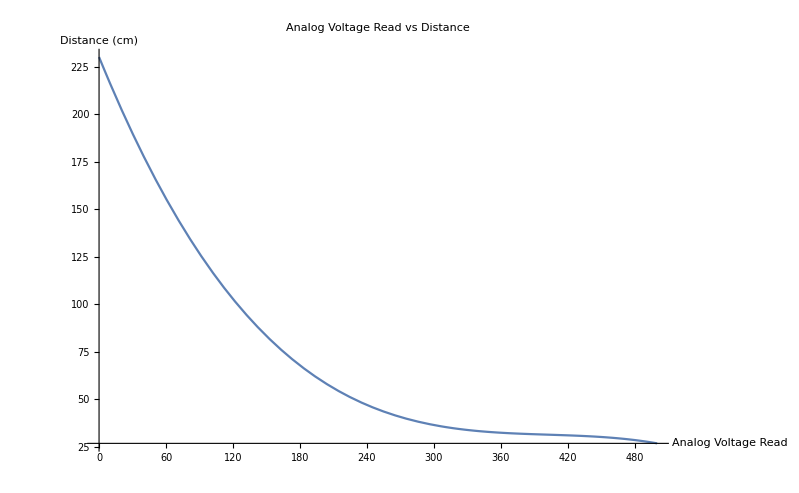

```mathematica
Plot[230.1430411867322-1.4451995839029892 x+0.0035444572391777783 x^2-2.9360497052173657*^-6 x^3,{x,0,500},PlotLabel->"Analog Voltage Read vs Distance",AxesLabel->{"Analog Voltage Read","Distance (cm)"}]
```

## Make Functions

### voltageToDistance takes input analog voltage read and returns distance in cm

```mathematica
voltageToDistance[x_]=(230.1430411867322-1.4451995839029892 x+0.0035444572391777783 x^2-2.9360497052173657*^-6 x^3);
```

### anglesToPan takes in the servo angles and converts to pan in degrees

```mathematica
anglesToPan[servo1_,servo2_]:=Module[{},(N@servo1-servo2)/2]
```

```mathematica
anglesToPan takes in the servo angles and converts to pan in degrees
```

```mathematica
anglesToTilt[servo1_,servo2_]:=Module[{},(N@servo1+servo2)/2]
```

### panTiltDistance takes in the servo positions and voltage and outputs the distance, tilt, and pan

```mathematica
panTiltDistance[{servo1_,servo2_,voltage_}]:=Module[{pan,tilt,distance},
pan=anglesToPan[servo1,servo2];
tilt=anglesToTilt[servo1,servo2];
distance=voltageToDistance[voltage];
Return[{distance,tilt,pan}]
]
```

### toCartesian takes in the distance, tilt, and pan and outputs Cartesian coordinates

```mathematica
ClearAll@toCartesian;
toCartesian[{distance_,tilt_,pan_}]:=Module[{radPan,radTilt,basePoint,panRotation,tiltRotation},
radPan=pan*π/180;
radTilt=tilt*π/180;
basePoint=distance*{1,0,0};
panRotation=RotationMatrix[radPan,{0,0,1}];
tiltRotation=RotationMatrix[radTilt,{0,1,0}];
tiltRotation.panRotation.basePoint
]
```

## Open Serial device and start reading data

### Open Arduino serial port

```mathematica
serial=DeviceOpen["Serial",{"/dev/ttyUSB1","BaudRate"->19200}]
```

DeviceObject[…]

### Clear the rawdata list to start capturing fresh scan data

```mathematica
rawdata={};
```

### Send a byte that contains 1 to the Arduino. This tells the Arduino to change state and start the scan procedure.

```mathematica
DeviceWrite[serial,1];
```

### Read a set number of data from the Arduino to rawdata. Magic numbers for various grid sizes: 1 degree = 3734

```mathematica
Do[AppendTo[rawdata,ToExpression[StringSplit[FromCharacterCode[DeviceReadBuffer[serial,"ReadTerminator"->10]],","]]],100]
Dynamic@Dimensions@rawdata
```

### Filter the raw data and make a 3d plot with pretty colors.

```mathematica
points=panTiltDistance/@rawdata;
points=Select[points,30<#[[1]]<80&];
points=toCartesian/@points;
ListPointPlot3D[points,ImageSize->Large,AxesLabel->{"x","y","z"},PlotStyle->PointSize[.03],ColorFunction->Function[{x,y,z},Hue[x/2]],AspectRatio->1]
```

-Graphics3D-

### Optional command to export good data

```mathematica
Export["filename",points,"Data"]
```

```mathematica
Length[rawdata]
```

100

# Close serial device

```mathematica
DeviceClose[serial]
```